```mathematica
savedir=SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes"];
```

```mathematica
NotebookSave[EvaluationNotebook[],savedir<>"\\uncertainty_dirichlet"]
```

```mathematica
nn=5*10^6;
```

```mathematica
data=Import["scripts\\dataset1_simple.csv"];
n=Length[data[[;;,1]]];
Dimensions[data]
```

{6029,97}

```mathematica
labels[ng_]:=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,1]];ClearAll[fs];fs[ng_]:=fs[ng]=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,2]]/n
```

```mathematica
fi=fs[{}]
```

{2427/6029,396/6029,1102/6029,443/6029,627/6029,73/6029,428/6029,533/6029}

```mathematica
bdistr[f_,nx_,aa_,t_,x_]=Block[{a1=aa+nx,f1=(nx*f+aa/t)/(nx+aa)},PDF[BetaDistribution[a1*f1,a1*(1-f1)],x]]
```

Piecewise[{{((1-x)^(-1+(aa+nx) (1-(f nx+aa/t)/(aa+nx))) x^(-1+f nx+aa/t))/Beta[f nx+aa/t,(aa+nx) (1-(f nx+aa/t)/(aa+nx))], 0<x<1}, {0, True}}]

```mathematica
eprob[f_,nx_,aa_,t_]=(nx*f+aa/t)/(nx+aa)
```

(f nx+aa/t)/(aa+nx)

```mathematica
ClearAll[ddir];ddir[nx_,f_,t_]:=ddir[nx,f,t]=Function[aa,
(*(Multinomial@@(nx*f))**)Gamma[aa]/Gamma[nx+aa]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^Length[f]]
```

```mathematica
ClearAll[lddir];lddir[nx_,f_,t_]:=lddir[nx,f,t]=Function[aa,
(*(Multinomial@@(nx*f))**)LogGamma[aa]-LogGamma[nx+aa]+(Total@LogGamma[nx*f+aa/t])-Length[f]*LogGamma[aa/t]]
```

```mathematica
listsample:=Block[{rsam=RandomSample[Range[94],25]},FoldList[Join,{rsam[[1]]},T@{rsam[[2;;]]}]]
```

```mathematica
listsample0=listsample;
```

```mathematica
ClearAll[lmaxi];lmaxi[f_,tx_]:=lmaxi[f,tx]={#[[1]],ax/.#[[2]]}&@NMaximize[{lddir[n,f,tx][ax]-Log[ax],1<ax<tx},ax,AccuracyGoal->Infinity,PrecisionGoal->4];
```

```mathematica
(*fun[ax_]=Simplify[ddir[n,fr,tx][ax]/ax/maxp];*)
ClearAll[inta,int1];inta[nx_,f_,tx_]:=inta[nx,f,tx]=Block[{maxf=Exp@lmaxi[f,tx][[1]]},NIntegrate[ddir[nx,f,tx][aa]/(nx+aa)/maxf,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]];
int1[nx_,f_,tx_]:=int1[nx,f,tx]=Block[{maxf=Exp@lmaxi[f,tx][[1]]},NIntegrate[ddir[nx,f,tx][aa]/aa/maxf,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]];
```

```mathematica
ef[nx_,f_,t_,fx_,tx_]:=f-(f-1/t)*inta[nx,fx,tx]/int1[nx,fx,tx]
```

```mathematica
ef[n,{0,1/n},2^(15),fs[listsample0[[15]]],2^(3+15)]
```

{0.0000146787,0.000100764}

```mathematica
tef=ef[n,fi,8,fs[listsample0[[15]]],2^(3+15)]
```

{0.269053,0.0942138,0.15499,0.0982598,0.114099,0.0664082,0.0969685,0.106007}

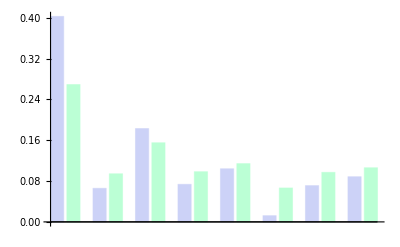

```mathematica
BarChart[T@{fi,tef}]
```

```mathematica
fi//N
```

{0.402554,0.0656825,0.182783,0.0734782,0.103997,0.0121081,0.0709902,0.088406}

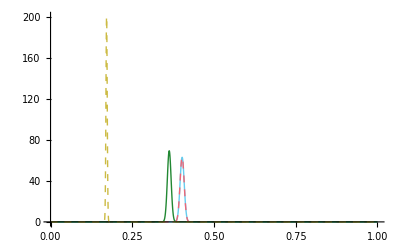

```mathematica
Plot[Evaluate@Table[bdistr[fi[[1]],n,aa,8,x],{aa,{0.1,1,1000,30000}}],{x,0,1},PlotRange->{0,All},PlotStyle->{Auto,Dashed}]
```

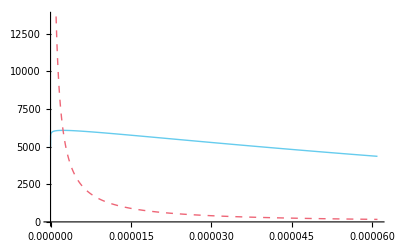

```mathematica
tt=2^15;Plot[Evaluate@Flatten@Table[{bdistr[1/n,n,aa,tt,x],bdistr[0,n,aa,tt,x]},{aa,{500}}],{x,0,2/tt},PlotRange->Auto,PlotStyle->{Auto,Dashed}]
```

```mathematica
eprob[{1/n,0},n,500,tt]
```

{8317/53485568,125/53485568}

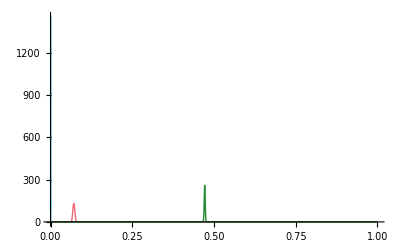

```mathematica
Plot[Evaluate@Table[bdistr[1/n,n,aa,x],{aa,{1,1000,10^5}}],{x,0,1},PlotRange->{0,All}]
```